```mathematica
Vivek Gupta|BA (Hons) Economics|20202948|Practical-3
```

## Plotting third order solution family of Differential Equation Question 1: Solve third order Differential Equation y''' - 5y'' + 8y' - 4y = 0 and Plot its three Solutions. Solution :

{{y[x]→ⅇ^x C[1]+ⅇ^(2 x) C[2]+ⅇ^(2 x) x C[3]}}

ⅇ^x+0.5 ⅇ^(2 x)+2/3 ⅇ^(2 x) x

-ⅇ^x/2+ⅇ^(2 x) x

-ⅇ^x-4 ⅇ^(2 x)+2 ⅇ^(2 x) x

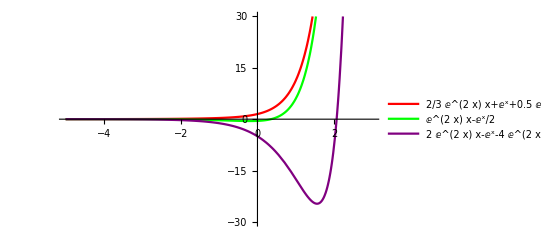

```mathematica
Sol=DSolve[y'''[x]-5 y''[x]+8 y'[x]-4 y[x] == 0,y[x],x]
Sol1=y[x]/.Sol⟦1⟧/.{C[1]->1,C[2]->0.5,C[3]->2/3}
Sol2=y[x]/.Sol⟦1⟧/.{C[1]->-1/2,C[2]->0,C[3]->1}
Sol3=y[x]/.Sol⟦1⟧/.{C[1]->-1,C[2]->-4,C[3]->2}
Plot[{Sol1,Sol2,Sol3},{x,-5,3},PlotRange->{-30,30},PlotStyle->{{Red},{Green},{Purple}},PlotLegends->{Sol1,Sol2,Sol3}]
```

## Question 2: Solve third order Differential Equation y’’’ + 3y’’ - 25y’ + 21y = 0 and Plot its any four Solutions. Solution :

21 y[x]-25 y'[x]+3 y''[x]+y^(3)[x]

{{y[x]→ⅇ^(-7 x) C[1]+ⅇ^x C[2]+ⅇ^(3 x) C[3]}}

ⅇ^(-7 x)+2 ⅇ^(3 x)

-1/2 ⅇ^(-7 x)+ⅇ^(3 x)

-ⅇ^(-7 x)-4 ⅇ^x+2 ⅇ^(3 x)

-0.5 ⅇ^(-7 x)-2 ⅇ^x+ⅇ^(3 x)

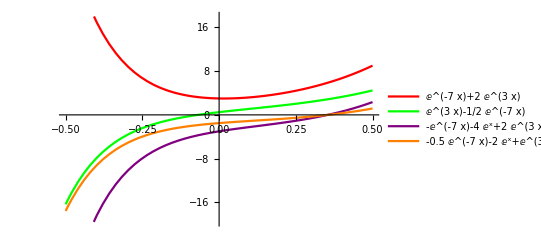

```mathematica
Eqn=y'''[x]+3*y''[x]-25*y'[x]+21*y[x]
Sol=DSolve[Eqn==0,y[x],x]
Sol1=y[x]/.Sol⟦1⟧/.{C[1]->1,C[2]->0,C[3]->2}
Sol2=y[x]/.Sol⟦1⟧/.{C[1]->-1/2,C[2]->0,C[3]->1}
Sol3=y[x]/.Sol⟦1⟧/.{C[1]->-1,C[2]->-4,C[3]->2}
Sol4=y[x]/.Sol⟦1⟧/.{C[1]->-0.5,C[2]->-2,C[3]->1}
Plot[{Sol1,Sol2,Sol3,Sol4},{x,-0.5,0.5},PlotStyle->{{Red},{Green},{Purple},{Orange}},PlotLegends->{Sol1,Sol2,Sol3,Sol4}]
```

## Question 3: Solve third order Differential Equation y’’’ - 4y’’ - 25y’ + 28y = 0 and Plot its any four Solutions. Solution :

28 y[x]-25 y'[x]-4 y''[x]+y^(3)[x]

{{y[x]→ⅇ^(-4 x) C[1]+ⅇ^x C[2]+ⅇ^(7 x) C[3]}}

ⅇ^(-4 x)+2 ⅇ^(7 x)

-2 ⅇ^(-4 x)+10 ⅇ^x+3 ⅇ^(7 x)

-ⅇ^(-4 x)-4 ⅇ^x+20 ⅇ^(7 x)

-0.5 ⅇ^(-4 x)-2 ⅇ^x+ⅇ^(7 x)

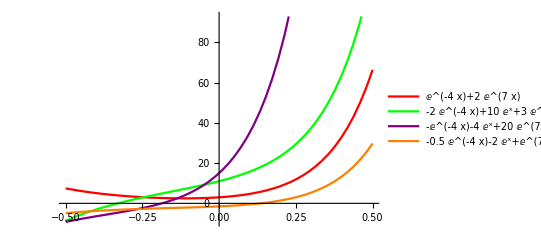

```mathematica
Eqn=y'''[x]-4*y''[x]-25*y'[x]+28*y[x]
Sol=DSolve[Eqn ==0,y[x],x]
Sol1=y[x]/.Sol⟦1⟧/.{C[1]->1,C[2]->0,C[3]->2}
Sol2=y[x]/.Sol⟦1⟧/.{C[1]->-2,C[2]->10,C[3]->3}
Sol3=y[x]/.Sol⟦1⟧/.{C[1]->-1,C[2]->-4,C[3]->20}
Sol4=y[x]/.Sol⟦1⟧/.{C[1]->-0.5,C[2]->-2,C[3]->1}
Plot[{Sol1,Sol2,Sol3,Sol4},{x,-0.5,0.5},PlotStyle->{{Red},{Green},{Purple},{Orange}},PlotLegends->{Sol1,Sol2,Sol3,Sol4}]
```